```mathematica
(*Potencial*)
V[x_,a_]:=x^2+x^4+a x
```

```mathematica
Vtilde[x_,a_,ψ_,g_]:=V[x,a]+g Abs[ψ]^2
```

```mathematica
ψ0[x_]:=(1/π)^(1/4)Exp[-1/2 x^2]HermiteH[0,x]
```

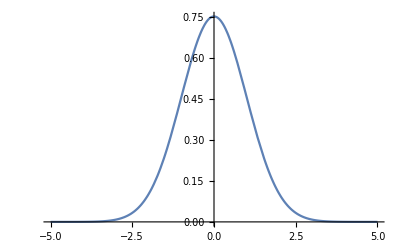

```mathematica
Plot[ψ0[x],{x,-5,5},PlotRange->All]
```

```mathematica
Vtilde[x,-1,ψ0[x],1]
```

(ⅇ^(-Re[x^2]))/(√π)-x+x^2+x^4

```mathematica
dt=0.01
```

0.01

```mathematica
ϕ=-ⅈ dt
```

0.-0.01 ⅈ

```mathematica
x=Table[i,{i,-10,10,0.1}];
```

```mathematica
psi0=ψ0[x];
```

```mathematica
ψ1=Exp[ϕ/2 Vtilde[x,-1,psi0,1]]psi0;
```

```mathematica
Fourier[ψ1];
```

```mathematica
ψ2k=Exp[ϕ]
```

ψ2k

## Calibración de las ks

```mathematica
ψprueba[x_]:=Exp[- x^2]
```

```mathematica
ψprueba[x_]:=PDF[NormalDistribution[0,1],x]
```

```mathematica
n=2^8;x0=-10.;xf=10;d=(xf-x0)/(n-1);
```

```mathematica
xprueba=Range[x0,xf,d];
```

```mathematica
xprueba//Length
```

256

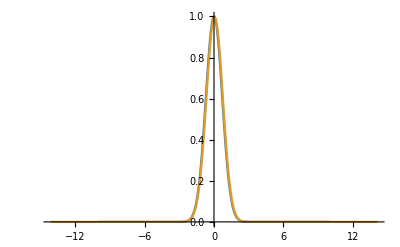

```mathematica
ft=Abs[Fourier[ψprueba[xprueba (9π)/20]]];
ftMaxValue=Max[ft];
ListPlot[{Transpose[{xprueba,ψprueba[xprueba]}],Transpose[{(9π)/20 xprueba,RotateLeft[ft/ftMaxValue,n/2]}]},PlotRange->All,Joined->True]
```

```mathematica
ψprueba[s]
```

ⅇ^(-s^2)

```mathematica
FourierTransform[ψprueba[s],s,t]
```

(ⅇ^(-t^2/4))/(√2)

```mathematica
RotateLeft[ft/ftMaxValue,n/2][[123;;133]]
```

{0.643406,0.736213,0.82202,0.895615,0.952183,0.987825,1.,0.987825,0.952183,0.895615,0.82202}

```mathematica
ψprueba[xprueba][[123;;133]]
```

{0.830205,0.882879,0.927414,0.962283,0.986255,0.998463,0.998463,0.986255,0.962283,0.927414,0.882879}

```mathematica
xprueba[[123;;133]]
```

{-0.431373,-0.352941,-0.27451,-0.196078,-0.117647,-0.0392157,0.0392157,0.117647,0.196078,0.27451,0.352941}